```mathematica
Лабораторная работа №7 Ковальчук В.В. ПО-4
```

```mathematica
Используем RandomVariate с NormalDistribution,чтобы сгенерировать последовательность из 20 чисел,следующих нормальному распределению со средним значением 0 и стандартным отклонением 1:
```

```mathematica
rnorms1=RandomVariate[NormalDistribution[0,1],20]
```

{2.18503,0.375687,0.778308,0.392957,0.355365,-0.466889,-1.02127,1.91588,-0.911474,-0.00366461,-1.12998,0.0542552,-1.82749,-1.438,-0.945128,1.29241,-1.07255,-0.149616,-0.850629,0.166777}

```mathematica
Используем ListPlot для визуализации данных:
```

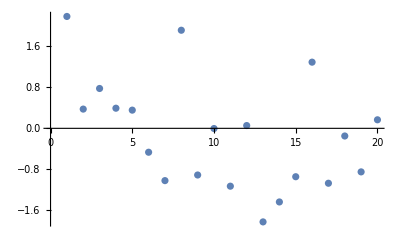

```mathematica
ListPlot[rnorms1]
```

```mathematica
Теперь можно построить случайное блуждание по данным:
```

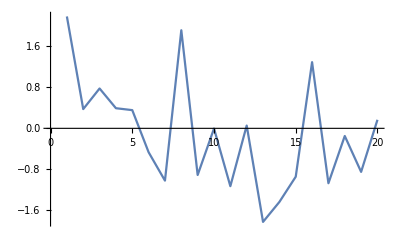

```mathematica
ListLinePlot[rnorms1]
```

```mathematica
Чтобы начать обход с нуля,добавим его в список:
```

```mathematica
rnorms2=Prepend[rnorms1,0]
```

{0,2.18503,0.375687,0.778308,0.392957,0.355365,-0.466889,-1.02127,1.91588,-0.911474,-0.00366461,-1.12998,0.0542552,-1.82749,-1.438,-0.945128,1.29241,-1.07255,-0.149616,-0.850629,0.166777}

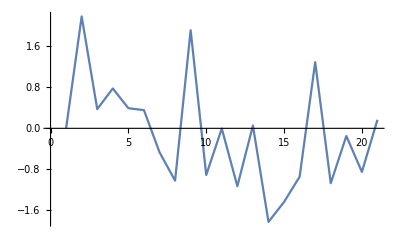

```mathematica
ListLinePlot[rnorms2]
```

```mathematica
Используем Accumulate для последовательного суммирования данных,которые затем визуализируются с помощью ListLinePlot:
```

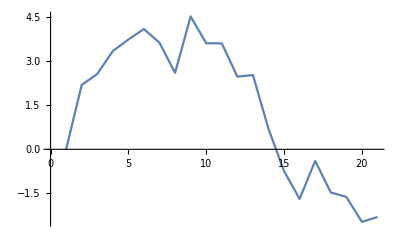

```mathematica
ListLinePlot[Accumulate[rnorms2]]
```

```mathematica
Определим функцию randomWalk,которая генерирует случайное блуждание длины n:
```

```mathematica
randomWalk[n_]:=Accumulate[Prepend[RandomVariate[NormalDistribution[0,1],n],0]]
```

```mathematica
Здесь Table используется для создания пяти случайных блужданий,каждое длиной 100. Затем они визуализируются с помощью ListLinePlot:
```

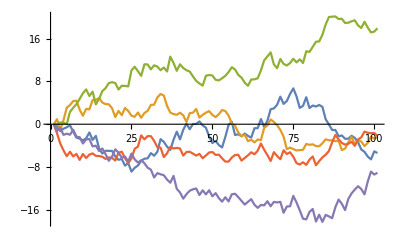

```mathematica
ListLinePlot[Table[randomWalk[100],{5}]]
```

```mathematica
Теперь сгенерируем 1000 обходов,каждый длиной 100. Вывод подавляется точкой с запятой (;),так как его не нужно видеть:
```

```mathematica
rwalks=Table[randomWalk[100],{1000}];
```

```mathematica
Теперь можно рассчитать описательную статистику по любому аспекту случайных блужданий.Здесь анализируется конечная позиция каждой прогулки. Используем[[]] (краткая форма функции Part),чтобы получить окончательную точку данных каждого случайного блуждания:
```

```mathematica
final=rwalks[[All,-1]];
```

```mathematica
Рассчитаем различные статистические данные по окончательным точкам данных из 1000 случайных блужданий:
```

```mathematica
{Mean[final],StandardDeviation[final],Max[final],Min[final]}
```

{0.421639,9.8134,28.3083,-33.389}

```mathematica
Методы Монте-Карло также можно использовать для аппроксимации значений,таких как константы или числовые интегралы.Например,следующее аппроксимирует значение,создавая случайные точки в квадрате вокруг круга радиусом 1,а затем используя соотношение между площадью квадрата и кругом.
```

```mathematica
Сгенерируем 10 000 точек в квадрате,ограниченном {-1,-1} и {1,1}:
```

```mathematica
pairs=RandomReal[{-1,1},{10000,2}];
```

```mathematica
Просмотрим сгенерированные точки:
```

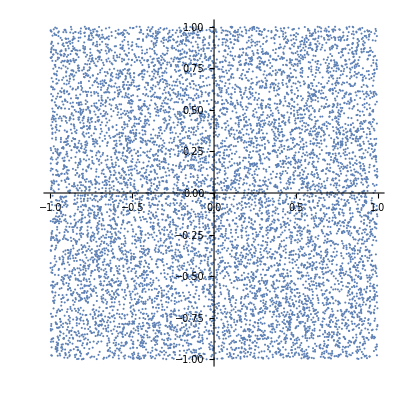

```mathematica
lp=ListPlot[pairs,AspectRatio->1]
```

```mathematica
Для приближения умножьте площадь квадрата на процент точек,попадающих в круг радиусом 1 с центром в начале координат.Умножьте площадь квадрата (4) на долю точек в круге:
```

```mathematica
4 Count[Map[Norm,pairs],_?(#≤1&)]/10000.
```

3.154

```mathematica
Использование большего количества точек или усреднение нескольких приближений обычно дает лучшее приближение.Определим функцию для аппроксимации выборки размером n:
```

```mathematica
approxPi[n_]:=4. Count[Map[Norm,RandomReal[{-1,1},{n,2}]],_?(#≤1&)]/n
```

```mathematica
с использованием миллиона точек:
```

```mathematica
approxPi[10^6]
```

3.14284

```mathematica
Аппроксимация путем усреднения 50 приближений из выборок размером 10000:
```

```mathematica
Mean[Table[approxPi[10000],{1000}]]
```

3.14147